```mathematica
fP[f1_,f2_,d_]:=(f1 f2)/(f1+f2-d)(1-d/f1) (*Focal plane wrt the second lens. Positive to the right of the lens*)
yim[f1_,f2_,d_,θ_]:=(f1 f2)/(f1+f2-d)θ (*Image height*)
```

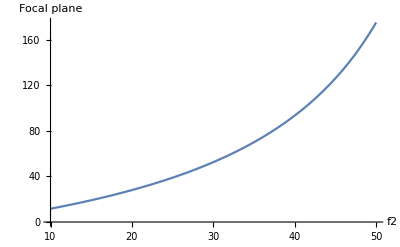

```mathematica
f1=60;
d=130; (*Inter-lens distance*)
θ=2 Degree;(*Incident angle*)
Plot[fP[f1,f2,d],{f2,10,50},AxesLabel->{"f2","Focal plane"}]
```

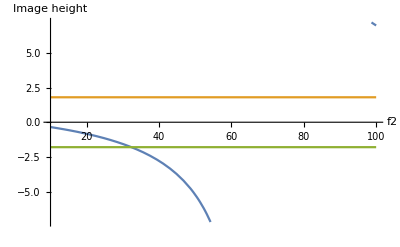

```mathematica
Plot[{yim[f1,f2,d,θ],1.8,-1.8},{f2,10,100},AxesLabel->{"f2","Image height"}]
```

```mathematica
f2=30;
1.fP[f1,f2,d]
1.yim[f1,f2,d,θ]
```

52.5

-1.5708